```mathematica
Quit[]
```

```mathematica
(* Definitions *)
```

```mathematica
(* Set the directory *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb];
(* data path *)
datapath=NotebookDirectory[];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(* Various scales and data *)
```

```mathematica
(* Various params *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
KtoeV=8.621738*10^-5;
cmtoeV=1/8065.544005;
ρcr…over…h2=8.098*10^-11 eV^4;
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_,wb_,wc_]:=w0+wa(1-a)+wb(1-a)^2+wc(1-a)^3
f[a_,w0_,wa_,wb_,wc_]:=a^(-3 (1+w0+wa+wb+wc)) ⅇ^(1/2 (-1+a) (6 wa-3 (-3+a) wb+(11+a (-7+2 a)) wc))
(*
 Tests: 
-1-1/3 a D[Log[f[a,w0,wa]],a]-w[a,w0,wa]//Simplify
Exp[-3Integrate[(1+w[aa,w0,wa])/aa,{aa,1,a},GenerateConditions->False]]//PowerExpand//FullSimplify
 *)
```

```mathematica
(* H(z) for the w0waCDM model *) 
Neff=3.044;
Ωγh2=Pi^2/30 gγ T^4/(ρcr…over…h2)/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV;
Ωγ[h_]:=Ωγh2/h^2;
Ων[h_,Neff_]:=Neff*7/8(4/11)^(4/3)Ωγ[h]
Ωr[h_,Neff_]:=Ωγ[h]+Ων[h,Neff];
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=100h Sqrt[om a^-3+Ωr[h,Neff] a^-4+(1-om-Ωr[h,Neff])f[a,w0,wa,wb,wc]]

(* Densities *)
ΩDE[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=((1-om-Ωr[h,Neff])f[a,w0,wa,wb,wc])/(H[a,om,w0,wa,wb,wc,h]/(100h))^2
Ωrel[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(Ωr[h,Neff] a^-4)/(H[a,om,w0,wa,wb,wc,h]/(100h))^2
Ωm[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(om a^-3)/(H[a,om,w0,wa,wb,wc,h]/(100h))^2
```

```mathematica
(* Sound speed, see Eq. (3.66) in the old version of Dodelson's book *)
cs[a_?NumberQ,obh2_?NumberQ]:=c Sqrt[1/(3(1+3/4 obh2/Ωγh2 a))]
(* Old expression from Wang's paper on CMB shift params *)
cs…old[a_?NumberQ,obh2_?NumberQ]:=c/√(3(1+(31500 obh2(Tcmb/2.7)^-4)a));
(* Redshift at decoupling (see Eqs. (66)-(68) in Komatsu et al.2009) *)
zcmb…EH[omh2_?NumberQ,obh2_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(omh2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift (see Eq. (4) of Hu astro-ph/9709112) *)
zdrag…EH[omh2_?NumberQ,obh2_?NumberQ]:=1291 omh2^0.251/(1+0.659 omh2^0.828)(1+(0.313(omh2)^-0.419(1+0.607 omh2^0.674))(obh2)^(0.238 omh2^0.223))
(* Redshift at decoupling Eq. (A4) from 2106.00428 *)
zcmb…GA[ωm_?NumberQ,ωb_?NumberQ]:=(391.672 ωm^(−0.372296)+937.422 ωb^(−0.97966))/(ωm^(−0.0192951) ωb^(−0.93681))+ωm^(−0.731631)
(* Redshift at decoupling Eq. (A2) from 2106.00428 *)
zdrag…GA[ωm_?NumberQ,ωb_?NumberQ]:=1/ωm^0.714129(1+428.169 ωb^0.256459 ωm^0.616388+925.56 ωm^0.751615)
```

```mathematica
(* Proper (not comoving) angular diameter distance with curvature, see Komatsu et al. 0803.0547 Eq. (2) zcmb[om,obh2] *)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(DLsol[om,w0,wa,wb,wc,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,wb,wc,h]/(100h)),dL[0]==0},dL,{zz,0,1500},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,w0,wa,wb,wc,h])[[1]]//Chop
```

```mathematica
(* Angular diameter distance, see Komatsu et al. 0803.0547  *)
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=1/(1+z)^2 DL[z,om,w0,wa,wb,wc,h]
(* rs approximation from Eisenstein and Hu, ApJ,496,605, Eq. (26) *)
rs…EH[omh2_,obh2_]:=44.5Log[9.83/omh2]/(√(1+10(obh2)^(3/4)));
(* Comoving sound horizon at drag redshift *)
rs…num[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=NIntegrate[cs[A,obh2]/(A^2H[A,om,w0,wa,wb,wc,h]),{A,0,1/(1+ze[om h^2,obh2])}]
(* Sound horizon from 2106.00428 *)
rsd…GA[ωm_,ωb_]:=Module[{a1=0.00257366,a2=0.05032,a3=0.013,a4=0.7720642,a5=0.24346362,a6=0.00641072,a7=0.5350899,a8=32.7525,a9=0.315473},1/(a1 ωb^a2+a3 ωb^a4 ωm^a5+a6 ωm^a7)-a8/ωm^a9]
(* Sound horizon from 2212.04522 *)
rsd…HGM[ωm_,ωb_]:=147.05 (ωm/0.1432)^-0.23(3.044/3.04)^-0.1(ωb/0.02236)^-0.13
(* Dilation scale *)
Dv[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(((1+z)DA[z,om,w0,wa,wb,wc,h] )^2  ((c*z)/H[1/(1+z),om,w0,wa,wb,wc,h]))^(1/3)
(* BAO Subscript[d, z] ratio *)
dz[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=rs…num[zdrag…GA,om,obh2,w0,wa,wb,wc,h]/Dv[z,om,w0,wa,wb,wc,h]
(* DH "distance" *)
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=c/H[1/(1+z),om,w0,wa,wb,wc,h]
(* Scaled distance at recombination *)
R[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=√(om (100h)^2)DA[zcmb…GA[om h^2,obh2],om,w0,wa,wb,wc,h](1+zcmb…GA[om h^2,obh2])/c
(* Angular scale of sound horizon at recombination *)
la[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=π (DA[zcmb…GA[om h^2,obh2],om,w0,wa,wb,wc,h](1+zcmb…GA[om h^2,obh2]))/(rs…num[zcmb…GA,om,obh2,w0,wa,wb,wc,h])

(* DM "distance" *)
DM[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=(1+z)DA[z,om,w0,wa,wb,wc,h]

(* DM "distance" ratio over rs(zd) *)
DM…over…rs[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=((1+z)DA[z,om,w0,wa,wb,wc,h])/rs…num[zdrag…GA,om,obh2,w0,wa,wb,wc,h]
```

```mathematica
(* end *)
```

```mathematica
(* CMB and BAO χ^2 terms *)
```

```mathematica
(* CMB: Planck18 *)
```

```mathematica
(* Central values and 1σ errors for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck 2018 for non-flat universe *)
(* See 1811.07425, page 7, Eq.(32) for details *)
datacmb={1.74451,301.76918,0.022483};
σCMB={0.093,0.0051,0.00016};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{2556.7782, 23212.222, -57.345815}, {23212.222, 830122.02, -628.56261}, {-57.345815, -628.56261, 2.5300094}});
invcov=Inverse[covcmb];
(* χ^2 for R *)
vec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:={R[om,obh2,w0,wa,wb,wc,h]-datacmb[[1]],la[om,obh2,w0,wa,wb,wc,h]-datacmb[[2]],obh2-datacmb[[3]]};
chi2…CMB[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=vec[om,obh2,w0,wa,wb,wc,h].invcov.vec[om,obh2,w0,wa,wb,wc,h]
```

```mathematica
(* BAO: DESI-Y1 *)
```

```mathematica
(* The errors of the data, see Table 1 in 2404.03002 *)
BGS…σ=0.15;
LRG…05…σ={0.25,0.61,-0.445};
LRG…07…σ={0.32,0.60,-0.420};
LRG…ELG…09…σ={0.28,0.35,-0.389};
ELG…13…σ={0.69,0.42,-0.444};
QSO…σ=0.67;
Lya…QSO…233…σ={0.94,0.17,-0.477};
(* The values *)
data…BAO={{0.30,7.93},{0.51,13.62},{0.51,20.98},{0.71,16.85},{0.71,20.08},{0.93,21.71},{0.93,17.88},{1.32,27.79},{1.32,13.82},{1.49,26.07},{2.33,39.71},{2.33,8.52}};
```

```mathematica
(* This makes the covariance/Fisher matrices *)
make…cij[vec_List]:={{vec[[1]]^2,vec[[1]] vec[[2]]vec[[3]]},{vec[[1]] vec[[2]]vec[[3]],vec[[2]]^2}}
make…cij[vec_]:=vec^2
Cij…DESI=ConstantArray[0,{12,12}];
Cij…DESI[[1,1]]=make…cij@BGS…σ;
Cij…DESI[[{2,3},{2,3}]]=make…cij@LRG…05…σ;
Cij…DESI[[{4,5},{4,5}]]=make…cij@LRG…07…σ;
Cij…DESI[[{6,7},{6,7}]]=make…cij@LRG…ELG…09…σ;
Cij…DESI[[{8,9},{8,9}]]=make…cij@ELG…13…σ;
Cij…DESI[[10,10]]=make…cij@QSO…σ;
Cij…DESI[[{11,12},{11,12}]]=make…cij@Lya…QSO…233…σ;
Fij…DESI=Inverse[Cij…DESI];
```

```mathematica
(* BBN prior *)
chi2…BBN…DESI[obh2_?NumberQ]:=((obh2-0.02218)/0.00055)^2

(* The chi^2 *)
chi2…BAO…DESI…Gil[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{V…data,V…theory,ΔV},V…theory={Dv[data…BAO[[1,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[2,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[3,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[4,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[5,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[6,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[7,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[8,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[9,1]],om,w0,wa,wb,wc,h],Dv[data…BAO[[10,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[11,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[12,1]],om,w0,wa,wb,wc,h]}/rsd…HGM[om h^2,obh2];
V…data=data…BAO[[All,2]];
ΔV=V…theory-V…data;
ΔV.Fij…DESI.ΔV]

chi2…BAO…DESI…GA[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{V…data,V…theory,ΔV},V…theory={Dv[data…BAO[[1,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[2,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[3,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[4,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[5,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[6,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[7,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[8,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[9,1]],om,w0,wa,wb,wc,h],Dv[data…BAO[[10,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[11,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[12,1]],om,w0,wa,wb,wc,h]}/rsd…GA[om h^2,obh2];
V…data=data…BAO[[All,2]];
ΔV=V…theory-V…data;
ΔV.Fij…DESI.ΔV]

(* The chi^2 *)
chi2…BAO…DESI…rdh[om_?NumberQ,rdh_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{V…data,V…theory,ΔV},V…theory=h{Dv[data…BAO[[1,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[2,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[3,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[4,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[5,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[6,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[7,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[8,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[9,1]],om,w0,wa,wb,wc,h],Dv[data…BAO[[10,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[11,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[12,1]],om,w0,wa,wb,wc,h]}/rdh;
V…data=data…BAO[[All,2]];
ΔV=V…theory-V…data;
DownValues[DLsol]=Take[DownValues[DLsol],-1];
ΔV.Fij…DESI.ΔV]

chi2…BAO…DESI…num[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{V…data,V…theory,ΔV},V…theory={Dv[data…BAO[[1,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[2,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[3,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[4,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[5,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[6,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[7,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[8,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[9,1]],om,w0,wa,wb,wc,h],Dv[data…BAO[[10,1]],om,w0,wa,wb,wc,h],DM[data…BAO[[11,1]],om,w0,wa,wb,wc,h],DH[data…BAO[[12,1]],om,w0,wa,wb,wc,h]}/rs…num[zdrag…GA,om,obh2,w0,wa,wb,wc,h];
V…data=data…BAO[[All,2]];
ΔV=V…theory-V…data;
ΔV.Fij…DESI.ΔV]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Pantheon+SHOES SnIa χ^2 term *)
```

```mathematica
(* Read the SnIa data *)
```

```mathematica
path=".//data//data_Pantheon_Plus_SH0ES//";
data…Pantheon…plus=Import[path<>"Pantheon+SH0ES.dat","Table"];
ndat…Pantheon…plus=Length[data…Pantheon…plus]-1;
file…covs="Pantheon+SH0ES_STAT+SYS.zip";
script…mcut=10;
z…plus…min=0.01;
(*z…plus…SHOES…min=0.023;*)
z…plus…SHOES…min=0.01;
```

```mathematica
(* The redshifts and magnitudes data *)
z…cmb=data…Pantheon…plus[[2;;-1,3]];
z…hel=data…Pantheon…plus[[2;;-1,7]];
Mb…corr=data…Pantheon…plus[[2;;-1,9]];
is…calibrator=data…Pantheon…plus[[2;;-1, 14]];
ceph…D=data…Pantheon…plus[[2;;-1,13]];
(* The "raw" covariance *)
Dij0…Stat…Sys = Import[path<>file…covs,{"ZIP","Pantheon+SH0ES_STAT+SYS.cov","List"}];
Cij…tot=Partition[Dij0…Stat…Sys[[2;;-1]],{Dij0…Stat…Sys[[1]]}];
Dij0…Stat…Sys=.
```

```mathematica
(* Pantheon+ chi^2 *)
```

```mathematica
(* We can easily find the position of the pointσ above z_min=0.01 *)
conditions…Pantheon…Plus=If[#>z…plus…min,1,0]&/@z…cmb;
pos…PP=Flatten[Position[conditions…Pantheon…Plus,val_/;val==1]];
(* The marginalized covariance *)
InvCovTotal…Pplus=Inverse[Cij…tot[[pos…PP,pos…PP]]];
Id…plus=ConstantArray[1,Length[pos…PP]];
```

```mathematica
chi2…Pantheon…plus…Marge[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ] := Module[{dist, Δm, A, B, Ee},
dist = Table[
If[z…cmb[[i]]>z…plus…min,5 Log10[(1+z…hel[[i]])/(1+z…cmb[[i]])DL[z…cmb[[i]],om,w0,wa,wb,wc,h]]+25,Nothing],{i, 1, ndat…Pantheon…plus}];
Δm=Mb…corr[[pos…PP]]-dist;
A=Δm.InvCovTotal…Pplus.Δm;
B=Δm.InvCovTotal…Pplus.Id…plus;
Ee=Id…plus.InvCovTotal…Pplus.Id…plus;
A+Log[Ee/(2Pi)]-B^2/Ee]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Combine all data (SnIa, CMB, BAO) *)
```

```mathematica
(* The number of data points *)
ndat…BAO…DESI=12;
ndat…CMB=Length[datacmb];
ndat…Pantheon…plus…effective=Table[If[z…cmb[[i]]>z…plus…min,1,Nothing],{i, 1, ndat…Pantheon…plus}]//Total;
ndat…tot…DESI=ndat…Pantheon…plus…effective+ndat…CMB+ndat…BAO…DESI;

(* The total chi^2 for the new data *)
chi2…total[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{chi20},chi20=chi2…CMB[om,obh2,w0,wa,wb,wc,h]+chi2…BAO…DESI…Gil[om,obh2,w0,wa,wb,wc,h]+chi2…Pantheon…plus…Marge[om,w0,wa,wb,wc,h];DownValues[DLsol]=DownValues[DLsol][[-2;;-1]];
If[Im[chi20]≠0,10^20,chi20]]

(* The individual parts of the chi^2 for the old data *)
chi2…total…vec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,wb_?NumberQ,wc_?NumberQ,h_?NumberQ]:=Module[{chi20},chi20={chi2…CMB[om,obh2,w0,wa,wb,wc,h],chi2…BAO…DESI…Gil[om,obh2,w0,wa,wb,wc,h],chi2…Pantheon…plus…Marge[om,w0,wa,wb,wc,h]};DownValues[DLsol]=DownValues[DLsol][[-2;;-1]];
chi20]
```

```mathematica
ndat…tot…DESI
```

1605

```mathematica
(* end *)
```

```mathematica
(* MCMC stuff *)
```

```mathematica
(* Some code borrowed from *)
"https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately";
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
plempty[{left_,right_}]:=Plot[0,{x,-1,1},Frame->True,Axes->False,PlotStyle->White,FrameStyle->{{left,right},{White,White}},FrameTicks->None];
pleint=plempty[{Automatic,White}];
pleout=plempty[{White,White}];
```

```mathematica
(* This is the jump function // Proposes the next point *)
jumpfunc[point_,s_]:=point+RandomVariate[NormalDistribution[0,s],Length[point]]
jumpfuncmat[point_,cijtest_]:=RandomVariate[MultinormalDistribution[point,cijtest]]
(* Δχ^2 for 2 params, up to 3σ *)
dx2=Table[2 InverseGammaRegularized[Nn/2,1-Erf[xσ/(√2)]]/.Nn->2//N,{xσ,1,3}];
mysymmetrize[Cij_]:=(Cij+Transpose[Cij])/2;
(* Contours+color from the MCMC // Uses ConvexHull // Advanced++ *)
Needs["ComputationalGeometry`"];
Off[CompiledFunction::cflist];
Confid2D[data_List,color_,inter_]:=Module[{cv,cv1,cv2,qq},cv=ConvexHull[data,AllPoints->True];cv1=data[[#]]&/@cv;cv2=Join[cv1,{cv1[[1]],cv1[[2]]}];qq=Show[Graphics[{color,FilledCurve[BSplineCurve[cv2,SplineDegree->inter,SplineKnots->"Unclamped"]],Antialiasing->True}],Frame->True];qq]
normalize[bins_,counts_]:=counts/Max[counts]
(* Convergence diagnostics *)
Rstatistic[chain_,param_,burnin_]:=Module[{n,m,W,B,Rminus1},
m=chain//Length;
n=Table[chain[[i,burnin;;-1,1,param]]//Length,{i,1,m}]//Mean;
W=Mean[Table[Variance[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
B=n Variance[Table[Mean[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
Rminus1=√((1-1/n)+1/n B/W)-1]
(* Utils *)
time[dt1_]:=Which[dt1<60,ToString[dt1]<>" secs",60≤dt1<1000,ToString[dt1/60.]<>" mins",1000≤dt1,ToString[dt1/3600.]<>" hrs"]
```

```mathematica
(* end *)
```

```mathematica
(* Cache *)
```

```mathematica
obh2pl=0.02225;
ompl=0.3153;
s8pl=0.8111;
hpl=67.36/100;
obh2…BBN=0.02218;
```

```mathematica
fminL={};
```

```mathematica
fminM1={};
```

```mathematica
(* end *)
```

```mathematica
(* Minimizations and MCMC *)
```

```mathematica
(* Minimize all data *)
```

```mathematica
?chi2…total
```

```mathematica
chi2…total[0.315,0.0222,-1,0,0,0,0.673]
chi2…total[0.315,0.0222,-1,0.1,0,0,0.673]
chi2…total[0.315,0.0222,-1,0.1,0.1,0,0.673]
chi2…total[0.315,0.0222,-1,0.1,0.1,0.1,0.673]
```

1440.59

1521.04

1614.8

1683.6

```mathematica
fminΛ=FindMinimum[chi2…total[om,obh2,-1,0,0,0,h],{om,0.31,0.311},{obh2,0.0222,0.02221},{h,0.67,0.673}]//AbsoluteTiming
```

{22.2243,{1431.37,{om→0.300032,obh2→0.0225582,h→0.685171}}}

```mathematica
fminw=FindMinimum[chi2…total[om,obh2,w,0,0,0,h],{om,0.32,0.321},{obh2,0.02225,0.022251},{w,-0.98,-0.981},{h,0.67,0.671}]//AbsoluteTiming
```

{43.7568,{1429.98,{om→0.304452,obh2→0.0226163,w→-0.968188,h→0.678554}}}

```mathematica
fminw…BBN=FindMinimum[chi2…total[om,obh2…BBN,w,0,0,0,h],{om,0.32,0.321},{w,-0.98,-0.981},{h,0.67,0.671}]//AbsoluteTiming
```

{20.7948,{1439.39,{om→0.309354,w→-0.99662,h→0.676308}}}

```mathematica
fminw0wa…BBN=FindMinimum[chi2…total[om,obh2…BBN,w0,wa,0,0,h],{om,0.31,0.311},{w0,-0.8,-0.81},{wa,-0.7,-0.71},{h,0.67,0.671}]//AbsoluteTiming
```

{38.0344,{1430.24,{om→0.308198,w0→-0.824317,wa→-0.794992,h→0.680526}}}

```mathematica
(* end *)
```

```mathematica
(* DESI tests *)
```

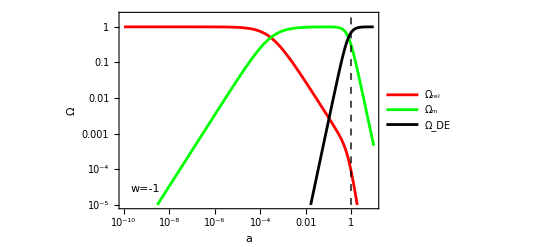

```mathematica
pp={a,ompl,-1,0,0,0,hpl};
LogLogPlot[{Ωrel@@pp,Ωm@@pp,ΩDE@@pp},{a,10^-10,10},Frame->True,FrameStyle->Black,FrameLabel->{"a","Ω"},PlotStyle->{Red,Green,Black},PlotLegends->{"Ω_rel","Ω_m","Ω_DE"},PlotRange->{10^-5,2},Epilog->{{Dashed,Line[{{1,10^-5},{1,5}}//Log]},Text["w=-1",Scaled[{0.1,.1}]]}]
```

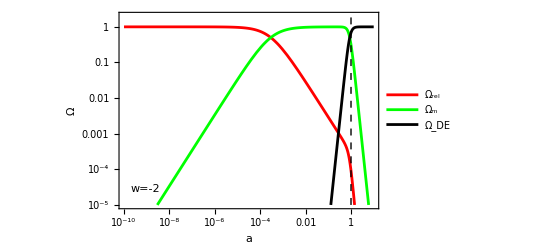

```mathematica
pp={a,ompl,-2,0,0,0,hpl};
LogLogPlot[{Ωrel@@pp,Ωm@@pp,ΩDE@@pp},{a,10^-10,10},Frame->True,FrameStyle->Black,FrameLabel->{"a","Ω"},PlotStyle->{Red,Green,Black},PlotLegends->{"Ω_rel","Ω_m","Ω_DE"},PlotRange->{10^-5,2},Epilog->{{Dashed,Line[{{1,10^-5},{1,5}}//Log]},Text["w=-2",Scaled[{0.1,.1}]]}]
```

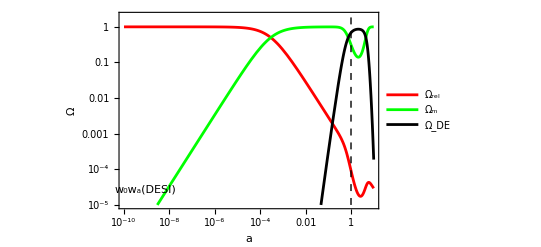

```mathematica
pp={a,ompl,−0.827,-0.75,0,0,hpl};
LogLogPlot[{Ωrel@@pp,Ωm@@pp,ΩDE@@pp},{a,10^-10,10},Frame->True,FrameStyle->Black,FrameLabel->{"a","Ω"},PlotStyle->{Red,Green,Black},PlotLegends->{"Ω_rel","Ω_m","Ω_DE"},PlotRange->{10^-5,2},Epilog->{{Dashed,Line[{{1,10^-5},{1,5}}//Log]},Text["w_0w_a(DESI)",Scaled[{0.1,.1}]]}]
```

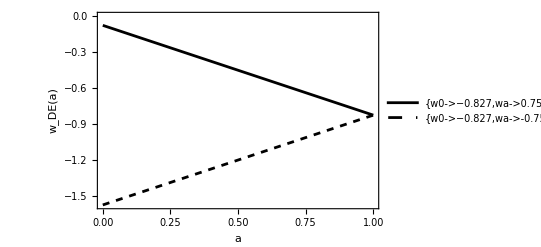

```mathematica
Plot[{w[a,w0,wa,0,0]/.{w0->−0.827,wa->0.75},w[a,w0,wa,0,0]/.{w0->−0.827,wa->-0.75}},{a,0,1},Frame->True,FrameStyle->Black,FrameLabel->{"a","w_DE(a)"},PlotStyle->{Black,{Dashed,Black}},PlotLegends->{"{w0->−0.827,wa->0.75}","{w0->−0.827,wa->-0.75}"}]
```

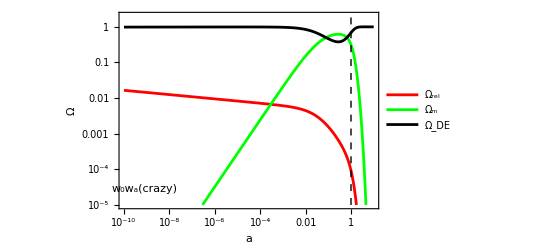

```mathematica
pp={a,ompl,−0.827,1.14,0,0,hpl};
LogLogPlot[{Ωrel@@pp,Ωm@@pp,ΩDE@@pp},{a,10^-10,10},Frame->True,FrameStyle->Black,FrameLabel->{"a","Ω"},PlotStyle->{Red,Green,Black},PlotLegends->{"Ω_rel","Ω_m","Ω_DE"},PlotRange->{10^-5,2},Epilog->{{Dashed,Line[{{1,10^-5},{1,5}}//Log]},Text["w_0w_a(crazy)",Scaled[{0.1,.1}]]}]
```

```mathematica
(* end *)
```

```mathematica
(* MCMC ΛCDM *)
```

```mathematica
(* Choose the params to vary *)
chi2[om_,h_]:=chi2…total[om,obh2…BBN,-1,0,0,0,h]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","h"};
priors={{0.2,0.4},{0.55,0.85}};
nparams=priors//Length;
smallchainname="smallchain_LCDM_v1";
bigchainname1="bigchain_LCDM_v1";
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain=Import[bigchainname1<>".zip",bigchainname1<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1439.41

{0.308746,0.677111}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.308858,0.677071}

{0.00473309,0.00321191}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.998,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.1*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000223491,-0.0000150684},{-0.0000150684,0.0000102941}}

True

True

{0.00472748,0.00320844}

```mathematica
params
```

{Ω_m,h}

```mathematica
MCMCchain=bigchain[[burnin;;-1]];
```

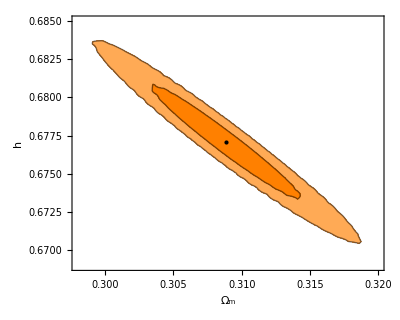

```mathematica
pp={1,2};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, 0.298,0.320},{b,0.669,0.685},Contours->cons,ContourShading->{White,Lighter[RGBColor[1,0.5,0]],RGBColor[1,0.5,0]},FrameLabel->{"Ω_m","h"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{0,-1},{0.5,-1}}]},{Dashed,Line[{{ompl,-2},{ompl,0}}]}}]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* MCMC wCDM *)
```

```mathematica
(* Choose the params to vary *)
chi2[om_,w_,h_]:=chi2…total[om,obh2…BBN,w,0,0,0,h]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","w","h"};
priors={{0.2,0.4},{-2,0},{0.55,0.85}};
nparams=priors//Length;
smallchainname="smallchain_wCDM_v1";
bigchainname1="bigchain_wCDM_v1";
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain=Import[bigchainname1<>".zip",bigchainname1<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1439.39

{0.309394,-0.996742,0.676303}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.309499,-0.997325,0.676355}

{0.00662185,0.0256756,0.00687739}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.998,1.02}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.1*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000437743,0.000117696,-0.0000430789},{0.000117696,0.000657908,-0.000155583},{-0.0000430789,-0.000155583,0.0000471732}}

True

True

{0.00661622,0.0256497,0.00686827}

```mathematica
θ={w};
Cijw0wa=Cijchain[[2,2]];
```

```mathematica
dw=D[w[a,w,0,0,0],{θ}]
ϵ={-1,0,1};
```

{1}

```mathematica
σw=Sqrt[Cijw0wa]//FullSimplify
```

0.0256497

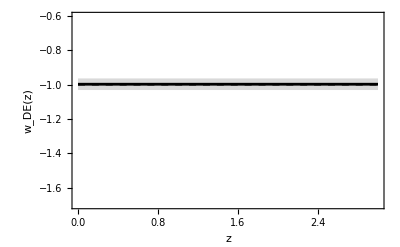

```mathematica
Plot[w[a,w,0,0,0]+ϵ σw/.a->1/(1+z)/.{w->bf[[2]]}//Evaluate,{z,0,3},Frame->True,FrameStyle->Black,PlotStyle->{LightGray,Black,LightGray},Filling->{1->{{3},LightGray}},PlotRange->{{0,3},{-1.7,-.6}},Epilog->{Dashed,Line[{{0,-1},{3,-1}}]},FrameLabel->{"z","w_DE(z)"}]
```

```mathematica
params
```

{Ω_m,w,h}

```mathematica
MCMCchain=bigchain[[burnin;;-1]];
```

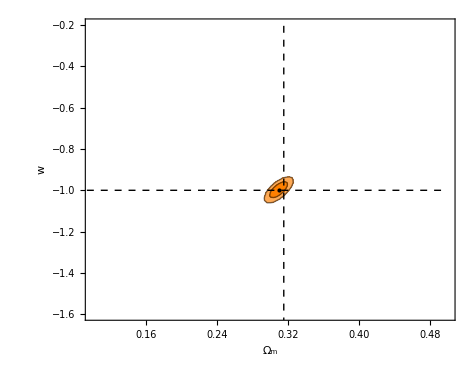

```mathematica
pp={1,2};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, 0.1,0.5},{b, -1.6, -0.2},Contours->cons,ContourShading->{White,Lighter[RGBColor[1,0.5,0]],RGBColor[1,0.5,0]},FrameLabel->{"Ω_m","w"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{0,-1},{0.5,-1}}]},{Dashed,Line[{{ompl,-2},{ompl,0}}]}}]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* MCMC w0-wa *)
```

```mathematica
(* Choose the params to vary *)
chi2[om_,w0_,wa_,h_]:=chi2…total[om,obh2…BBN,w0,wa,0,0,h]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","w_0","w_a","h"};
priors={{0.001,1},{-1.5,0},{-3,0.5},{0.5,1}};
nparams=priors//Length;
smallchainname="smallchain_w0wa_v1";
bigchainname1="bigchain_w0wa_v1";
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain=Import[bigchainname1<>".zip",bigchainname1<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1430.24

{0.308297,-0.82092,-0.806888,0.680427}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.308119,-0.817039,-0.843628,0.680955}

{0.00677242,0.0650642,0.2964,0.00721353}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.998,1.03}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.01*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000459351,0.0000926796,0.000199148,-0.0000462116},{0.0000926796,0.00423636,-0.0173449,-0.0000691526},{0.000199148,-0.0173449,0.0879531,-0.000527405},{-0.0000462116,-0.0000691526,-0.000527405,0.0000521143}}

True

True

{0.00677755,0.0650874,0.296569,0.00721902}

```mathematica
θ={w0,wa};
Cijw0wa=Cijchain[[{2,3},{2,3}]];
```

```mathematica
dw=D[w[a,w0,wa,0,0],{θ}]
ϵ={-1,0,1};
```

{1,1-a}

```mathematica
σw=Sqrt[dw.Cijw0wa.dw]//FullSimplify
```

√(0.0574996+(-0.141216+0.0879531 a) a)

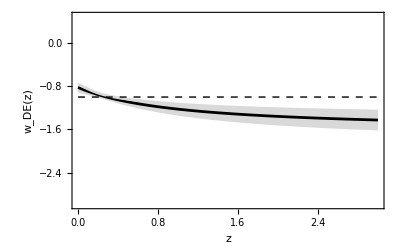

```mathematica
Plot[w[a,w0,wa,0,0]+ϵ σw/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]]}//Evaluate,{z,0,3},Frame->True,FrameStyle->Black,PlotStyle->{LightGray,Black,LightGray},Filling->{1->{{3},LightGray}},PlotRange->{{0,3},{-3,0.5}},Epilog->{Dashed,Line[{{0,-1},{3,-1}}]},FrameLabel->{"z","w_DE(z)"},Axes->False]
```

```mathematica
w…av[zmax_]:=zmax^-1 NIntegrate[w[a,w0,wa,0,0]/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]]},{z,0,zmax}]
```

```mathematica
Table[{zmax->zz,w…av[zz]},{zz,{1,2,3,1100}}]
```

{{zmax→1,-1.06852},{zmax→2,-1.18458},{zmax→3,-1.25495},{zmax→1100,-1.62267}}

```mathematica
w…av…weight[zmax_]:=NIntegrate[σw w[a,w0,wa,0,0]/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]]},{z,0,zmax}]/NIntegrate[σw/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]]},{z,0,zmax}]
```

```mathematica
Table[{zmax->zz,w…av…weight[zz]},{zz,{1,2,3,1100}}]
```

{{zmax→1,-1.09938},{zmax→2,-1.2398},{zmax→3,-1.31295},{zmax→1100,-1.62348}}

```mathematica
(*MCMCchain=bigchain[[burnin;;-1]]/.{{Ωmh2_,Ωbh2_,h_},chi20_}->{{Ωmh2/h^2,Ωbh2/h^2,h},chi20};*)
```

```mathematica
MCMCchain=bigchain[[burnin;;-1]];
```

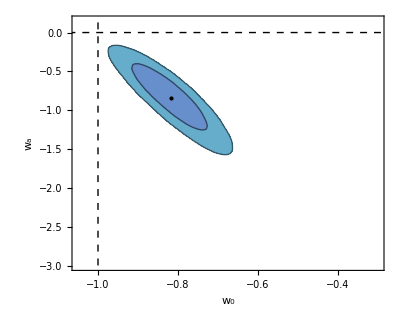

```mathematica
pp={2,3};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, -1.05,-0.3},{b, -3, 0.15},Contours->cons,ContourShading->{White,Hue[0.55,0.5,0.8],Hue[0.6,0.5,0.8]},FrameLabel->{"w_0","w_a"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{-1,-5},{-1,5}}]},{Dashed,Line[{{-5,0},{5,0}}]}}]
```

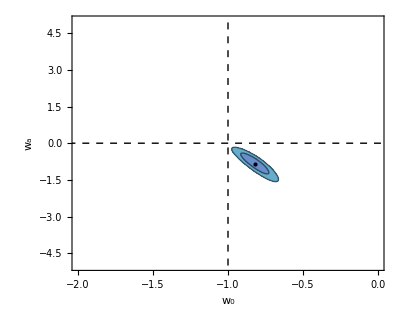

```mathematica
Show[con1,PlotRange->{{-2,0},{-5,5}}]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* MCMC w0-wa-wb *)
```

```mathematica
(* Choose the params to vary *)
chi2[om_,w0_,wa_,wb_,h_]:=chi2…total[om,obh2…BBN,w0,wa,wb,0,h]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","w_0","w_a","w_b","h"};
priors = {{0.2,0.4}, {-2,0}, {-5,5}, {-15,4}, {0.55,0.85}};
nparams=priors//Length;
smallchainname="smallchain_w0wawb_v1";
bigchainname1="bigchain_w0wawb_v1";
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain=Import[bigchainname1<>".zip",bigchainname1<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1428.98

{0.307012,-0.952969,0.705318,-2.89421,0.68293}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.306503,-0.99261,1.22548,-4.05221,0.683918}

{0.00694465,0.146771,1.57581,3.09847,0.00770864}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.1*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000481348,0.00024666,-0.00180283,0.00437771,-0.0000504016},{0.00024666,0.0215487,-0.220061,0.396963,-0.000353971},{-0.00180283,-0.220061,2.48592,-4.75959,0.00305873},{0.00437771,0.396963,-4.75959,9.60421,-0.00768559},{-0.0000504016,-0.000353971,0.00305873,-0.00768559,0.0000591914}}

True

True

{0.00693793,0.146795,1.57668,3.09907,0.00769359}

```mathematica
θ={w0,wa,wb};
Cijw0wa=Cijchain[[{2,3,4},{2,3,4}]];
```

```mathematica
dw=D[w[a,w0,wa,wb,0],{θ}]
ϵ={-1,0,1};
```

{1,1-a,(1-a)^2}

```mathematica
σw=Sqrt[dw.Cijw0wa.dw]//FullSimplify
```

√(2.9463+a (-15.9789+a (32.3476+a (-28.8977+9.60421 a))))

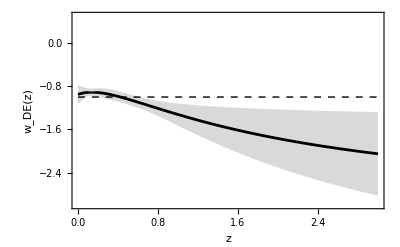

```mathematica
Plot[w[a,w0,wa,wb,0]+ϵ σw/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]],wb->bf[[4]]}//Evaluate,{z,0,3},Frame->True,FrameStyle->Black,PlotStyle->{LightGray,Black,LightGray},Filling->{1->{{3},LightGray}},PlotRange->{{0,3},{-3,0.5}},Epilog->{Dashed,Line[{{0,-1},{3,-1}}]},FrameLabel->{"z","w_DE(z)"},Axes->False]
```

```mathematica
(*MCMCchain=bigchain[[burnin;;-1]]/.{{Ωmh2_,Ωbh2_,h_},chi20_}->{{Ωmh2/h^2,Ωbh2/h^2,h},chi20};*)
```

```mathematica
MCMCchain=bigchain[[burnin;;-1]];
```

```mathematica
params
priors
```

{Ω_m,w_0,w_a,w_b,h}

{{0.2,0.4},{-2,0},{-5,5},{-15,4},{0.55,0.85}}

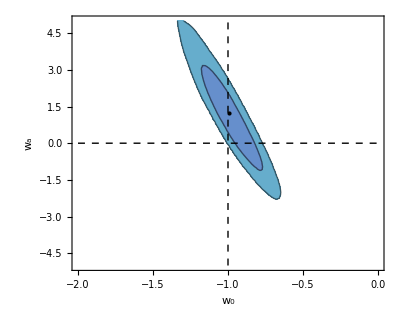

```mathematica
pp={2,3};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, -2,0},{b, -5, 5},Contours->cons,ContourShading->{White,Hue[0.55,0.5,0.8],Hue[0.6,0.5,0.8]},FrameLabel->{"w_0","w_a"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{-1,-5},{-1,5}}]},{Dashed,Line[{{-2,0},{0,0}}]}}]
```

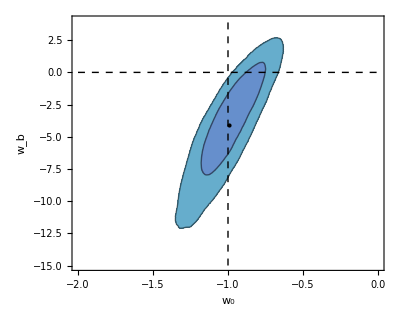

```mathematica
pp={2,4};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, -2,0},{b, -15, 4},Contours->cons,ContourShading->{White,Hue[0.55,0.5,0.8],Hue[0.6,0.5,0.8]},FrameLabel->{"w_0","w_b"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{-1,-15},{-1,5}}]},{Dashed,Line[{{-2,0},{0,0}}]}}]
```

```mathematica
(* Rescale Subscript[Ω, b] h^2 to 100*Subscript[Ω, b] h^2 to avoid problems with the graphics *)
mcmcchain=bigchain;
(* The parameters of the chains as they will appear in the plot and some default (Planck) values *)
def={ompl,-1,0,0,hpl};
(* Calculate the ranges of the plots and number of ticks (default ndivs+1). Set the fontsize. *)
fontsize=12;
ndivs=5;
nmax=Length[params];
lims=Table[{Min[mcmcchain[[All,1,i]]],Max[mcmcchain[[All,1,i]]]},{i,1,nmax}];
divs=Table[FindDivisions[lims[[i]],ndivs]//N,{i,1,nmax}];
ranges=lims/.{x_,y_}->{.987 x,1.015y};
```

```mathematica
(* This makes the 1D, 2D plots and the Triangle plot *)
pl1d[i_]:=SmoothHistogram[mcmcchain[[All,1,i]],Automatic,"PDF",Frame->True,PlotRange->{ranges[[i]],All},AspectRatio->1,FrameLabel->{params[[i]],None},FrameTicks->{{None,None},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,Axes->False,FrameStyle->Black,PlotStyle->Black,Epilog->{Black,Dashed,Line[{{def[[i]],0},{def[[i]],10^5}}]}]
pl2d[i_,j_]:=Module[{datapl,skd,pdf,cons,cenp},
datapl=mcmcchain[[All,1,{i,j}]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[{1,2,3}/(√2)]//N];
cenp=datapl//Mean;
ContourPlot[PDF[skd,{a,b}],{a, ranges[[i,1]],ranges[[i,2]]},{b, ranges[[j,1]], ranges[[j,2]]},Contours->cons,ContourShading->{White,Hue[0.6,0.5,0.8],Hue[0.55,0.5,0.8],Hue[0.5,0.5,0.9]},FrameLabel->params[[{i,j}]],FrameTicks->{{divs[[j]],Transpose[{divs[[j]],Table["",Length[divs[[j]]]]}]},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{Black,Point[cenp]},{Red,Point[{def[[i]],def[[j]]}]}}]]
tab[i_,j_]:=Which[i==j,pl1d[i],i<j,pl2d[i,j],i==j+1,pleint,True,pleout]
```

```mathematica
LaunchKernels[7];
```

```mathematica
(* Create the plots // most time is spent here hence parallelize *)
allplots=ParallelTable[tab[i,j],{j,1,nmax},{i,1,nmax}];
```

```mathematica
finalplot=Rasterize[Show[plotGrid[allplots,500,500,ImagePadding->45]],RasterSize->2000,ImageSize->600]
```

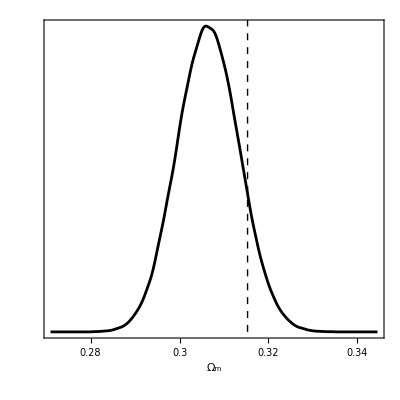
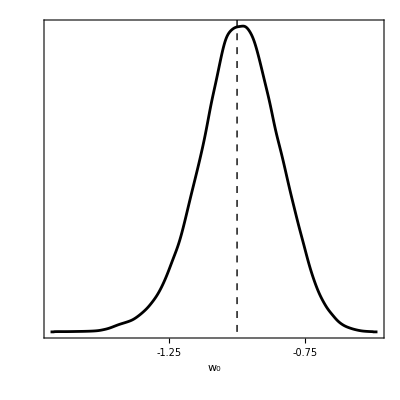
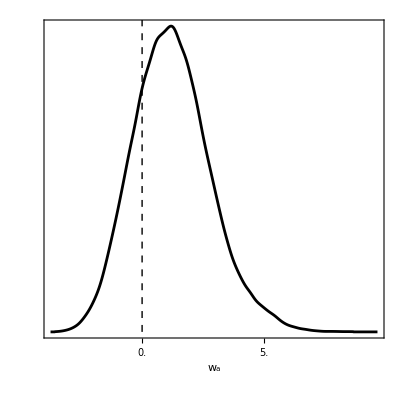
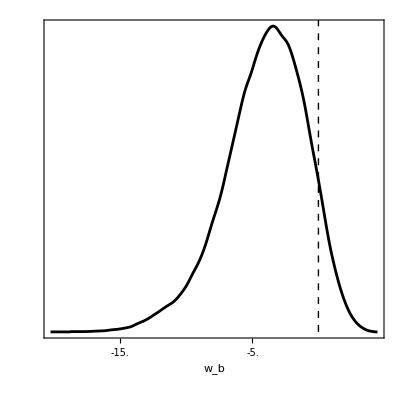
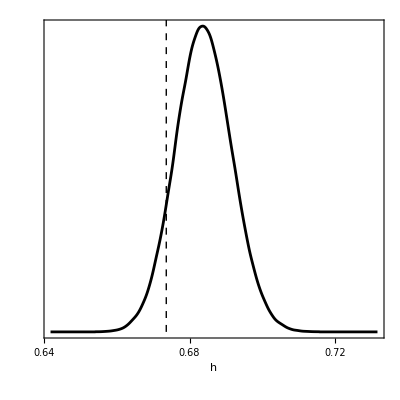

```mathematica
Table[pl1d[i],{i,1,nmax}]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* MCMC w0-wa-wb-wc *)
```

```mathematica
(* Choose the params to vary *)
chi2[om_,w0_,wa_,wb_,wc_,h_]:=chi2…total[om,obh2…BBN,w0,wa,wb,0,h]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","w_0","w_a","w_b","w_c","h"};
priors = {{0.2, 0.4},{-2, 0},{-20, 10},{-30,50},{-60,30},{0.55,0.75}};
nparams=priors//Length;
smallchainname="smallchain_w0wawbwc_v1";
bigchainname1="bigchain_w0wawbwc_v1";
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain0=Import["./old/"<>bigchainname1<>".zip",bigchainname1<>".m"];
bigchain1=Import[bigchainname1<>".zip",bigchainname1<>".m"];
```

```mathematica
bigchain=Join[bigchain0[[Round[0.01*Length[bigchain0]];;-1]],bigchain1[[Round[0.1*Length[bigchain1]];;-1]]];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1428.81

{0.310025,-0.994753,1.83717,-9.29314,8.70334,0.683478}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.306632,-0.966281,0.397445,0.99741,-7.52374,0.684327}

{0.00709392,0.182421,2.72171,10.7795,13.0055,0.00783589}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
Cijchain=Covariance[bigchain[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000503236,0.000385643,-0.00456727,0.016813,-0.0144153,-0.000052451},{0.000385643,0.0332776,-0.460667,1.50844,-1.3477,-0.000475576},{-0.00456727,-0.460667,7.4077,-27.5247,27.7822,0.00549304},{0.016813,1.50844,-27.5247,116.198,-132.58,-0.018082},{-0.0144153,-1.3477,27.7822,-132.58,169.142,0.0107545},{-0.000052451,-0.000475576,0.00549304,-0.018082,0.0107545,0.0000614012}}

True

True

{0.00709392,0.182421,2.72171,10.7795,13.0055,0.00783589}

```mathematica
params
```

{Ω_m,w_0,w_a,w_b,w_c,h}

```mathematica
θ={w0,wa,wb,wc};
Cij=Cijchain[[{2,3,4,5},{2,3,4,5}]];
```

```mathematica
dw=D[w[a,w0,wa,wb,wc],{θ}]
ϵ={-1,0,1};
```

{1,1-a,(1-a)^2,(1-a)^3}

```mathematica
σw=Sqrt[dw.Cij.dw]//FullSimplify
```

√(27.5349+a (-222.789+a (753.283+a (-1360.53+a (1383.09+a (-749.69+169.142 a))))))

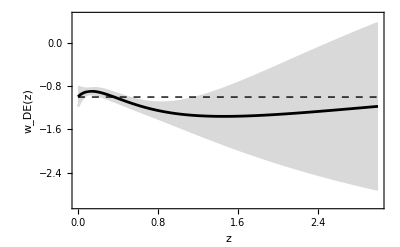

```mathematica
Plot[w[a,w0,wa,wb,wc]+ϵ σw/.a->1/(1+z)/.{w0->bf[[2]],wa->bf[[3]],wb->bf[[4]],wc->bf[[5]]}//Evaluate,{z,0,3},Frame->True,FrameStyle->Black,PlotStyle->{LightGray,Black,LightGray},Filling->{1->{{3},LightGray}},PlotRange->{{0,3},{-3,0.5}},Epilog->{Dashed,Line[{{0,-1},{3,-1}}]},FrameLabel->{"z","w_DE(z)"},Axes->False]
```

```mathematica
(*MCMCchain=bigchain[[burnin;;-1]]/.{{Ωmh2_,Ωbh2_,h_},chi20_}->{{Ωmh2/h^2,Ωbh2/h^2,h},chi20};*)
```

```mathematica
MCMCchain=bigchain;
```

```mathematica
params
priors
```

{Ω_m,w_0,w_a,w_b,w_c,h}

{{0.2,0.4},{-2,0},{-5,5},{-20,10},{-30,20},{0.55,0.85}}

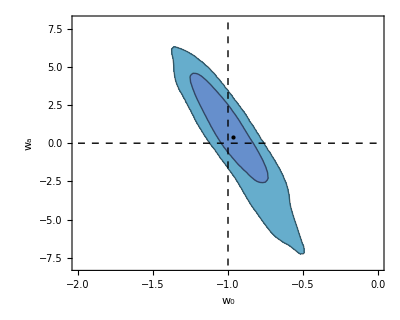

```mathematica
pp={2,3};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, -2,0},{b, -8, 8},Contours->cons,ContourShading->{White,Hue[0.55,0.5,0.8],Hue[0.6,0.5,0.8]},FrameLabel->{"w_0","w_a"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{-1,-8},{-1,8}}]},{Dashed,Line[{{-2,0},{0,0}}]}}]
```

```mathematica
priors
```

{{0.2,0.4},{-2,0},{-5,5},{-20,10},{-30,20},{0.55,0.85}}

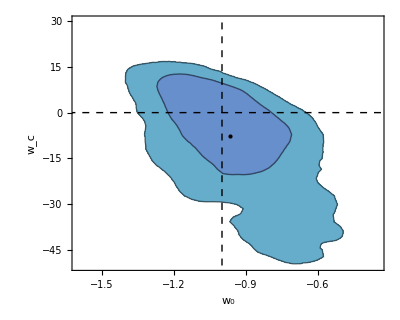

```mathematica
pp={2,5};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, -1.6,-0.35},{b, -50, 30},Contours->cons,ContourShading->{White,Hue[0.55,0.5,0.8],Hue[0.6,0.5,0.8]},FrameLabel->{"w_0","w_c"},BaseStyle->FontSize->14,PlotRange->All,FrameStyle->Black,ClippingStyle->None,AspectRatio->0.8,Epilog->{{Black,Point[cenp]},{Dashed,Line[{{-1,-50},{-1,50}}]},{Dashed,Line[{{-2,0},{0,0}}]}}]
```

```mathematica
(* Rescale Subscript[Ω, b] h^2 to 100*Subscript[Ω, b] h^2 to avoid problems with the graphics *)
mcmcchain=bigchain;
(* The parameters of the chains as they will appear in the plot and some default (Planck) values *)
def={ompl,-1,0,0,0,hpl};
(* Calculate the ranges of the plots and number of ticks (default ndivs+1). Set the fontsize. *)
fontsize=12;
ndivs=5;
nmax=Length[params];
lims=Table[{Min[mcmcchain[[All,1,i]]],Max[mcmcchain[[All,1,i]]]},{i,1,nmax}];
divs=Table[FindDivisions[lims[[i]],ndivs]//N,{i,1,nmax}];
ranges=lims/.{x_,y_}->{.987 x,1.015y};
```

```mathematica
(* This makes the 1D, 2D plots and the Triangle plot *)
pl1d[i_]:=SmoothHistogram[mcmcchain[[All,1,i]],Automatic,"PDF",Frame->True,PlotRange->{ranges[[i]],All},AspectRatio->1,FrameLabel->{params[[i]],None},FrameTicks->{{None,None},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,Axes->False,FrameStyle->Black,PlotStyle->Black,Epilog->{Black,Dashed,Line[{{def[[i]],0},{def[[i]],10^5}}]}]
pl2d[i_,j_]:=Module[{datapl,skd,pdf,cons,cenp},
datapl=mcmcchain[[All,1,{i,j}]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[{1,2,3}/(√2)]//N];
cenp=datapl//Mean;
ContourPlot[PDF[skd,{a,b}],{a, ranges[[i,1]],ranges[[i,2]]},{b, ranges[[j,1]], ranges[[j,2]]},Contours->cons,ContourShading->{White,Hue[0.6,0.5,0.8],Hue[0.55,0.5,0.8],Hue[0.5,0.5,0.9]},FrameLabel->params[[{i,j}]],FrameTicks->{{divs[[j]],Transpose[{divs[[j]],Table["",Length[divs[[j]]]]}]},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{Black,Point[cenp]},{Red,Point[{def[[i]],def[[j]]}]}}]]
tab[i_,j_]:=Which[i==j,pl1d[i],i<j,pl2d[i,j],i==j+1,pleint,True,pleout]
```

```mathematica
LaunchKernels[7];
```

```mathematica
(* Create the plots // most time is spent here hence parallelize *)
allplots=ParallelTable[tab[i,j],{j,1,nmax},{i,1,nmax}];
```

```mathematica
finalplot=Rasterize[Show[plotGrid[allplots,500,500,ImagePadding->45]],RasterSize->2000,ImageSize->600]
```

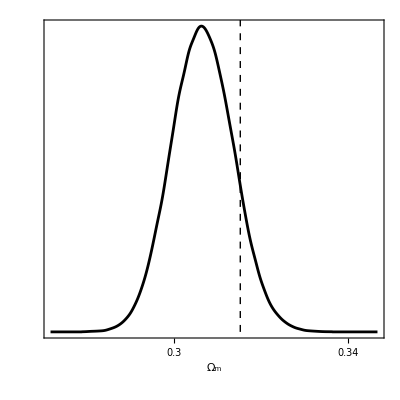
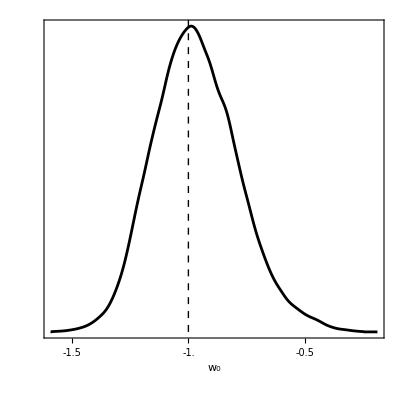
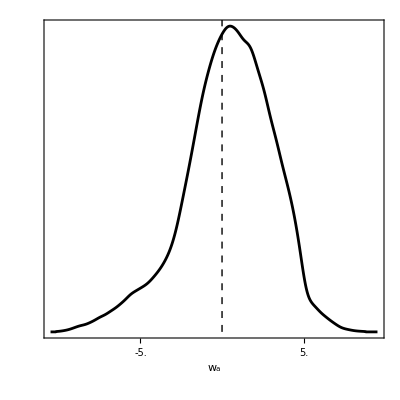
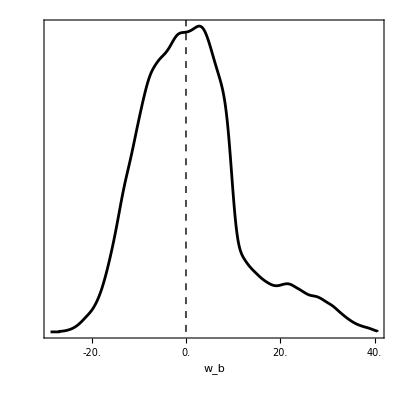
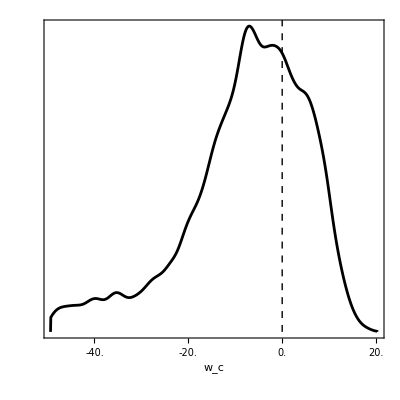
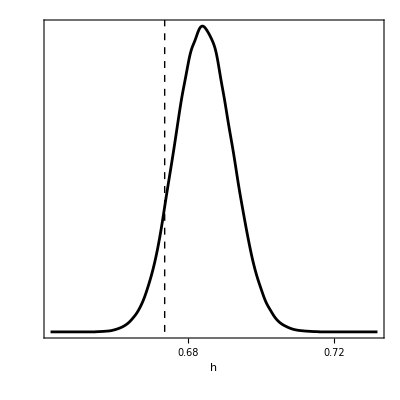

```mathematica
Table[pl1d[i],{i,1,nmax}]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Other plots *)
```

```mathematica
(* end  *)
```